```mathematica
BasicSet={a,b,b,c}
```

{a,b,b,c}

```mathematica
3^6
```

729

```mathematica
BasicSet$Tuples=Tuples[{BasicSet,BasicSet,BasicSet,BasicSet,BasicSet,BasicSet}];
%//Length
```

4096

```mathematica
BasicSet$Tuples//Union;
%//Length
```

729

```mathematica
BasicSet$Tuples$Union=Map[Sort[#]&,BasicSet$Tuples]//Union
%//Length
```

{{a,a,a,a,a,a},{a,a,a,a,a,b},{a,a,a,a,a,c},{a,a,a,a,b,b},{a,a,a,a,b,c},{a,a,a,a,c,c},{a,a,a,b,b,b},{a,a,a,b,b,c},{a,a,a,b,c,c},{a,a,a,c,c,c},{a,a,b,b,b,b},{a,a,b,b,b,c},{a,a,b,b,c,c},{a,a,b,c,c,c},{a,a,c,c,c,c},{a,b,b,b,b,b},{a,b,b,b,b,c},{a,b,b,b,c,c},{a,b,b,c,c,c},{a,b,c,c,c,c},{a,c,c,c,c,c},{b,b,b,b,b,b},{b,b,b,b,b,c},{b,b,b,b,c,c},{b,b,b,c,c,c},{b,b,c,c,c,c},{b,c,c,c,c,c},{c,c,c,c,c,c}}

28

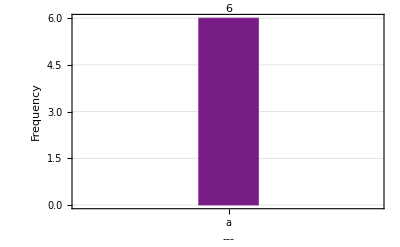
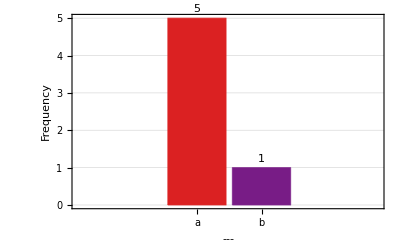
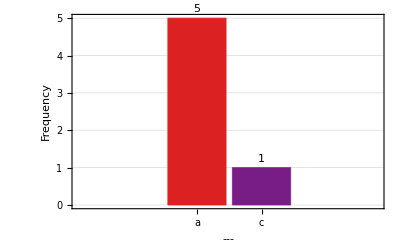
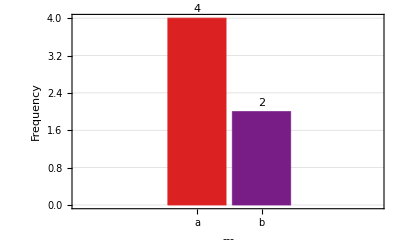
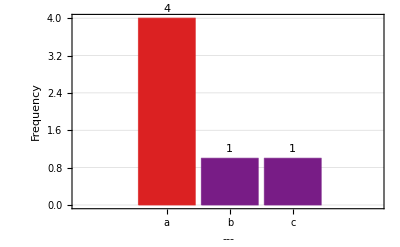
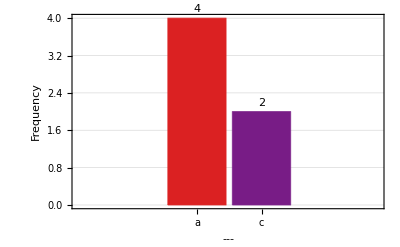
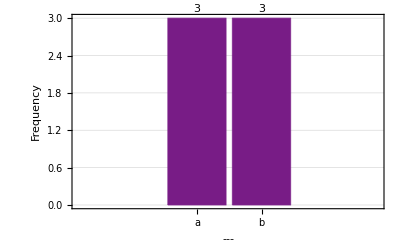
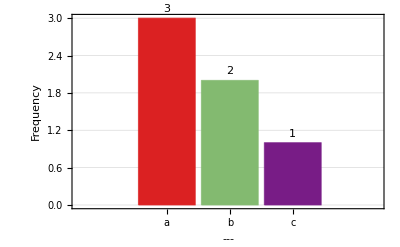
( | 1 | 2 | 3 | 4 | 5
1 | {a,a,a,a,a,a} | {{a,6}} | {6} | {a} | -Graphics-
2 | {a,a,a,a,a,b} | {{a,5},{b,1}} | {5,1} | {a,b} | -Graphics-
3 | {a,a,a,a,a,c} | {{a,5},{c,1}} | {5,1} | {a,c} | -Graphics-
4 | {a,a,a,a,b,b} | {{a,4},{b,2}} | {4,2} | {a,b} | -Graphics-
5 | {a,a,a,a,b,c} | {{a,4},{b,1},{c,1}} | {4,1,1} | {a,b,c} | -Graphics-
6 | {a,a,a,a,c,c} | {{a,4},{c,2}} | {4,2} | {a,c} | -Graphics-
7 | {a,a,a,b,b,b} | {{a,3},{b,3}} | {3,3} | {a,b} | -Graphics-
8 | {a,a,a,b,b,c} | {{a,3},{b,2},{c,1}} | {3,2,1} | {a,b,c} | -Graphics-
9 | {a,a,a,b,c,c} | {{a,3},{b,1},{c,2}} | {3,1,2} | {a,b,c} | -Graphics-
10 | {a,a,a,c,c,c} | {{a,3},{c,3}} | {3,3} | {a,c} | -Graphics-
11 | {a,a,b,b,b,b} | {{a,2},{b,4}} | {2,4} | {a,b} | -Graphics-
12 | {a,a,b,b,b,c} | {{a,2},{b,3},{c,1}} | {2,3,1} | {a,b,c} | -Graphics-
13 | {a,a,b,b,c,c} | {{a,2},{b,2},{c,2}} | {2,2,2} | {a,b,c} | -Graphics-
14 | {a,a,b,c,c,c} | {{a,2},{b,1},{c,3}} | {2,1,3} | {a,b,c} | -Graphics-
15 | {a,a,c,c,c,c} | {{a,2},{c,4}} | {2,4} | {a,c} | -Graphics-
16 | {a,b,b,b,b,b} | {{a,1},{b,5}} | {1,5} | {a,b} | -Graphics-
17 | {a,b,b,b,b,c} | {{a,1},{b,4},{c,1}} | {1,4,1} | {a,b,c} | -Graphics-
18 | {a,b,b,b,c,c} | {{a,1},{b,3},{c,2}} | {1,3,2} | {a,b,c} | -Graphics-
19 | {a,b,b,c,c,c} | {{a,1},{b,2},{c,3}} | {1,2,3} | {a,b,c} | -Graphics-
20 | {a,b,c,c,c,c} | {{a,1},{b,1},{c,4}} | {1,1,4} | {a,b,c} | -Graphics-
21 | {a,c,c,c,c,c} | {{a,1},{c,5}} | {1,5} | {a,c} | -Graphics-
22 | {b,b,b,b,b,b} | {{b,6}} | {6} | {b} | -Graphics-
23 | {b,b,b,b,b,c} | {{b,5},{c,1}} | {5,1} | {b,c} | -Graphics-
24 | {b,b,b,b,c,c} | {{b,4},{c,2}} | {4,2} | {b,c} | -Graphics-
25 | {b,b,b,c,c,c} | {{b,3},{c,3}} | {3,3} | {b,c} | -Graphics-
26 | {b,b,c,c,c,c} | {{b,2},{c,4}} | {2,4} | {b,c} | -Graphics-
27 | {b,c,c,c,c,c} | {{b,1},{c,5}} | {1,5} | {b,c} | -Graphics-
28 | {c,c,c,c,c,c} | {{c,6}} | {6} | {c} | -Graphics-)

```mathematica
MatrixForm[Map[{
#,
H1=Tally[#],
H1PureData=H1[[All,2]],
H1DataLabels=H1[[All,1]],
BarChart[H1PureData,ChartLabels->Map[Rotate[#,0 Degree]&,H1DataLabels],GridLines->Automatic,Frame->True,FrameLabel->{"---","Frequency"},ColorFunction->Function[{height},ColorData["Rainbow"][height]],LabelingFunction->(Placed[#,Above]&),PlotRangePadding->Scaled[.05],ImageSize->400]
}&,BasicSet$Tuples$Union],TableHeadings->Automatic,TableAlignments->Left]
```

```mathematica
XXX=Tally[Map[Sort[#]&,BasicSet$Tuples]]
%//Length
```

{{{a,a,a,a,a,a},1},{{a,a,a,a,a,b},12},{{a,a,a,a,a,c},6},{{a,a,a,a,b,b},60},{{a,a,a,a,b,c},60},{{a,a,a,a,c,c},15},{{a,a,a,b,b,b},160},{{a,a,a,b,b,c},240},{{a,a,a,b,c,c},120},{{a,a,a,c,c,c},20},{{a,a,b,b,b,b},240},{{a,a,b,b,b,c},480},{{a,a,b,b,c,c},360},{{a,a,b,c,c,c},120},{{a,a,c,c,c,c},15},{{a,b,b,b,b,b},192},{{a,b,b,b,b,c},480},{{a,b,b,b,c,c},480},{{a,b,b,c,c,c},240},{{a,b,c,c,c,c},60},{{a,c,c,c,c,c},6},{{b,b,b,b,b,b},64},{{b,b,b,b,b,c},192},{{b,b,b,b,c,c},240},{{b,b,b,c,c,c},160},{{b,b,c,c,c,c},60},{{b,c,c,c,c,c},12},{{c,c,c,c,c,c},1}}

28

{{{a,a,a,a,a,a},1},{{a,a,a,a,a,b},12},{{a,a,a,a,a,c},6},{{a,a,a,a,b,b},60},{{a,a,a,a,b,c},60},{{a,a,a,a,c,c},15},{{a,a,a,b,b,b},160},{{a,a,a,b,b,c},240},{{a,a,a,b,c,c},120},{{a,a,a,c,c,c},20},{{a,a,b,b,b,b},240},{{a,a,b,b,b,c},480},{{a,a,b,b,c,c},360},{{a,a,b,c,c,c},120},{{a,a,c,c,c,c},15},{{a,b,b,b,b,b},192},{{a,b,b,b,b,c},480},{{a,b,b,b,c,c},480},{{a,b,b,c,c,c},240},{{a,b,c,c,c,c},60},{{a,c,c,c,c,c},6},{{b,b,b,b,b,b},64},{{b,b,b,b,b,c},192},{{b,b,b,b,c,c},240},{{b,b,b,c,c,c},160},{{b,b,c,c,c,c},60},{{b,c,c,c,c,c},12},{{c,c,c,c,c,c},1}}

{1,12,6,60,60,15,160,240,120,20,240,480,360,120,15,192,480,480,240,60,6,64,192,240,160,60,12,1}

{{a,a,a,a,a,a},{a,a,a,a,a,b},{a,a,a,a,a,c},{a,a,a,a,b,b},{a,a,a,a,b,c},{a,a,a,a,c,c},{a,a,a,b,b,b},{a,a,a,b,b,c},{a,a,a,b,c,c},{a,a,a,c,c,c},{a,a,b,b,b,b},{a,a,b,b,b,c},{a,a,b,b,c,c},{a,a,b,c,c,c},{a,a,c,c,c,c},{a,b,b,b,b,b},{a,b,b,b,b,c},{a,b,b,b,c,c},{a,b,b,c,c,c},{a,b,c,c,c,c},{a,c,c,c,c,c},{b,b,b,b,b,b},{b,b,b,b,b,c},{b,b,b,b,c,c},{b,b,b,c,c,c},{b,b,c,c,c,c},{b,c,c,c,c,c},{c,c,c,c,c,c}}

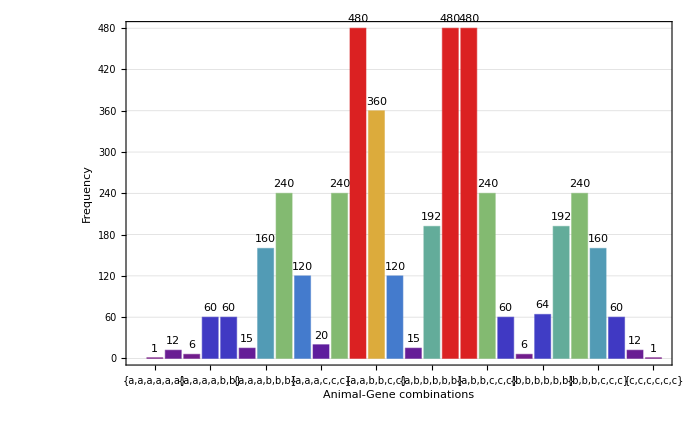

```mathematica
DataAct=XXX
PureData=DataAct[[All,2]]
DataLabels=DataAct[[All,1]]
BarChart[PureData,ChartLabels->Map[Rotate[#,45 Degree]&,DataLabels],GridLines->Automatic,Frame->True,FrameLabel->{"Animal-Gene combinations","Frequency"},ColorFunction->Function[{height},ColorData["Rainbow"][height]],LabelingFunction->(Placed[#,Above]&),PlotRangePadding->Scaled[.05],ImageSize->700]
```

```mathematica
YYY=Sort[Tally[Map[Sort[#]&,BasicSet$Tuples]],#1[[2]]>#2[[2]]&]
%//Length
```

{{{a,b,b,b,c,c},480},{{a,b,b,b,b,c},480},{{a,a,b,b,b,c},480},{{a,a,b,b,c,c},360},{{b,b,b,b,c,c},240},{{a,b,b,c,c,c},240},{{a,a,b,b,b,b},240},{{a,a,a,b,b,c},240},{{b,b,b,b,b,c},192},{{a,b,b,b,b,b},192},{{b,b,b,c,c,c},160},{{a,a,a,b,b,b},160},{{a,a,b,c,c,c},120},{{a,a,a,b,c,c},120},{{b,b,b,b,b,b},64},{{b,b,c,c,c,c},60},{{a,b,c,c,c,c},60},{{a,a,a,a,b,c},60},{{a,a,a,a,b,b},60},{{a,a,a,c,c,c},20},{{a,a,c,c,c,c},15},{{a,a,a,a,c,c},15},{{b,c,c,c,c,c},12},{{a,a,a,a,a,b},12},{{a,c,c,c,c,c},6},{{a,a,a,a,a,c},6},{{c,c,c,c,c,c},1},{{a,a,a,a,a,a},1}}

28

```mathematica
MatrixForm[YYY]
```

({a,b,b,b,c,c} | 480
{a,b,b,b,b,c} | 480
{a,a,b,b,b,c} | 480
{a,a,b,b,c,c} | 360
{b,b,b,b,c,c} | 240
{a,b,b,c,c,c} | 240
{a,a,b,b,b,b} | 240
{a,a,a,b,b,c} | 240
{b,b,b,b,b,c} | 192
{a,b,b,b,b,b} | 192
{b,b,b,c,c,c} | 160
{a,a,a,b,b,b} | 160
{a,a,b,c,c,c} | 120
{a,a,a,b,c,c} | 120
{b,b,b,b,b,b} | 64
{b,b,c,c,c,c} | 60
{a,b,c,c,c,c} | 60
{a,a,a,a,b,c} | 60
{a,a,a,a,b,b} | 60
{a,a,a,c,c,c} | 20
{a,a,c,c,c,c} | 15
{a,a,a,a,c,c} | 15
{b,c,c,c,c,c} | 12
{a,a,a,a,a,b} | 12
{a,c,c,c,c,c} | 6
{a,a,a,a,a,c} | 6
{c,c,c,c,c,c} | 1
{a,a,a,a,a,a} | 1)

{{{a,b,b,b,c,c},480},{{a,b,b,b,b,c},480},{{a,a,b,b,b,c},480},{{a,a,b,b,c,c},360},{{b,b,b,b,c,c},240},{{a,b,b,c,c,c},240},{{a,a,b,b,b,b},240},{{a,a,a,b,b,c},240},{{b,b,b,b,b,c},192},{{a,b,b,b,b,b},192},{{b,b,b,c,c,c},160},{{a,a,a,b,b,b},160},{{a,a,b,c,c,c},120},{{a,a,a,b,c,c},120},{{b,b,b,b,b,b},64},{{b,b,c,c,c,c},60},{{a,b,c,c,c,c},60},{{a,a,a,a,b,c},60},{{a,a,a,a,b,b},60},{{a,a,a,c,c,c},20},{{a,a,c,c,c,c},15},{{a,a,a,a,c,c},15},{{b,c,c,c,c,c},12},{{a,a,a,a,a,b},12},{{a,c,c,c,c,c},6},{{a,a,a,a,a,c},6},{{c,c,c,c,c,c},1},{{a,a,a,a,a,a},1}}

{480,480,480,360,240,240,240,240,192,192,160,160,120,120,64,60,60,60,60,20,15,15,12,12,6,6,1,1}

{{a,b,b,b,c,c},{a,b,b,b,b,c},{a,a,b,b,b,c},{a,a,b,b,c,c},{b,b,b,b,c,c},{a,b,b,c,c,c},{a,a,b,b,b,b},{a,a,a,b,b,c},{b,b,b,b,b,c},{a,b,b,b,b,b},{b,b,b,c,c,c},{a,a,a,b,b,b},{a,a,b,c,c,c},{a,a,a,b,c,c},{b,b,b,b,b,b},{b,b,c,c,c,c},{a,b,c,c,c,c},{a,a,a,a,b,c},{a,a,a,a,b,b},{a,a,a,c,c,c},{a,a,c,c,c,c},{a,a,a,a,c,c},{b,c,c,c,c,c},{a,a,a,a,a,b},{a,c,c,c,c,c},{a,a,a,a,a,c},{c,c,c,c,c,c},{a,a,a,a,a,a}}

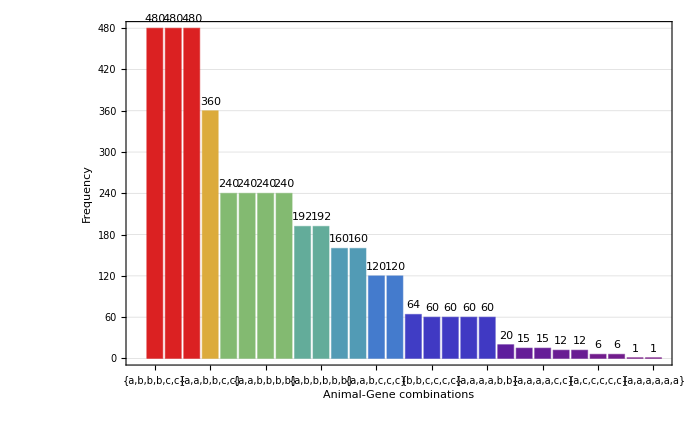

```mathematica
DataAct=YYY
PureData=DataAct[[All,2]]
DataLabels=DataAct[[All,1]]
BarChart[PureData,ChartLabels->Map[Rotate[#,45 Degree]&,DataLabels],GridLines->Automatic,Frame->True,FrameLabel->{"Animal-Gene combinations","Frequency"},ColorFunction->Function[{height},ColorData["Rainbow"][height]],LabelingFunction->(Placed[#,Above]&),PlotRangePadding->Scaled[.05],ImageSize->700]
```

```mathematica
MatrixForm[YYY]
```

({a,b,b,b,c,c} | 480
{a,b,b,b,b,c} | 480
{a,a,b,b,b,c} | 480
{a,a,b,b,c,c} | 360
{b,b,b,b,c,c} | 240
{a,b,b,c,c,c} | 240
{a,a,b,b,b,b} | 240
{a,a,a,b,b,c} | 240
{b,b,b,b,b,c} | 192
{a,b,b,b,b,b} | 192
{b,b,b,c,c,c} | 160
{a,a,a,b,b,b} | 160
{a,a,b,c,c,c} | 120
{a,a,a,b,c,c} | 120
{b,b,b,b,b,b} | 64
{b,b,c,c,c,c} | 60
{a,b,c,c,c,c} | 60
{a,a,a,a,b,c} | 60
{a,a,a,a,b,b} | 60
{a,a,a,c,c,c} | 20
{a,a,c,c,c,c} | 15
{a,a,a,a,c,c} | 15
{b,c,c,c,c,c} | 12
{a,a,a,a,a,b} | 12
{a,c,c,c,c,c} | 6
{a,a,a,a,a,c} | 6
{c,c,c,c,c,c} | 1
{a,a,a,a,a,a} | 1)

```mathematica
YYY
```

{{{a,b,b,b,c,c},480},{{a,b,b,b,b,c},480},{{a,a,b,b,b,c},480},{{a,a,b,b,c,c},360},{{b,b,b,b,c,c},240},{{a,b,b,c,c,c},240},{{a,a,b,b,b,b},240},{{a,a,a,b,b,c},240},{{b,b,b,b,b,c},192},{{a,b,b,b,b,b},192},{{b,b,b,c,c,c},160},{{a,a,a,b,b,b},160},{{a,a,b,c,c,c},120},{{a,a,a,b,c,c},120},{{b,b,b,b,b,b},64},{{b,b,c,c,c,c},60},{{a,b,c,c,c,c},60},{{a,a,a,a,b,c},60},{{a,a,a,a,b,b},60},{{a,a,a,c,c,c},20},{{a,a,c,c,c,c},15},{{a,a,a,a,c,c},15},{{b,c,c,c,c,c},12},{{a,a,a,a,a,b},12},{{a,c,c,c,c,c},6},{{a,a,a,a,a,c},6},{{c,c,c,c,c,c},1},{{a,a,a,a,a,a},1}}

```mathematica
Map[#&,YYY]
```

{{{a,b,b,b,c,c},480},{{a,b,b,b,b,c},480},{{a,a,b,b,b,c},480},{{a,a,b,b,c,c},360},{{b,b,b,b,c,c},240},{{a,b,b,c,c,c},240},{{a,a,b,b,b,b},240},{{a,a,a,b,b,c},240},{{b,b,b,b,b,c},192},{{a,b,b,b,b,b},192},{{b,b,b,c,c,c},160},{{a,a,a,b,b,b},160},{{a,a,b,c,c,c},120},{{a,a,a,b,c,c},120},{{b,b,b,b,b,b},64},{{b,b,c,c,c,c},60},{{a,b,c,c,c,c},60},{{a,a,a,a,b,c},60},{{a,a,a,a,b,b},60},{{a,a,a,c,c,c},20},{{a,a,c,c,c,c},15},{{a,a,a,a,c,c},15},{{b,c,c,c,c,c},12},{{a,a,a,a,a,b},12},{{a,c,c,c,c,c},6},{{a,a,a,a,a,c},6},{{c,c,c,c,c,c},1},{{a,a,a,a,a,a},1}}

```mathematica
Total[Map[{Count[#[[1]],a],#[[2]]}&,YYY][[All,2]]]
```

4096

```mathematica
MatrixForm[Map[{Count[#[[1]],a],#[[2]]}&,YYY]]
```

(1 | 480
1 | 480
2 | 480
2 | 360
0 | 240
1 | 240
2 | 240
3 | 240
0 | 192
1 | 192
0 | 160
3 | 160
2 | 120
3 | 120
0 | 64
0 | 60
1 | 60
4 | 60
4 | 60
3 | 20
2 | 15
4 | 15
0 | 12
5 | 12
1 | 6
5 | 6
0 | 1
6 | 1)

```mathematica
Select[Map[{Count[#[[1]],a],#[[2]]}&,YYY],#[[1]]===1&]
```

{{1,480},{1,480},{1,240},{1,192},{1,60},{1,6}}

```mathematica
MatrixForm[Table[Select[Map[{Count[#[[1]],a],#[[2]]}&,YYY],#[[1]]===i&],{i,0,6}],TableHeadings->Automatic,TableAlignments->Left]
```

(1 | {{0,240},{0,192},{0,160},{0,64},{0,60},{0,12},{0,1}}
2 | {{1,480},{1,480},{1,240},{1,192},{1,60},{1,6}}
3 | {{2,480},{2,360},{2,240},{2,120},{2,15}}
4 | {{3,240},{3,160},{3,120},{3,20}}
5 | {{4,60},{4,60},{4,15}}
6 | {{5,12},{5,6}}
7 | {{6,1}})

```mathematica
Y1=Table[Select[Map[{Count[#[[1]],a],#[[2]]}&,YYY],#[[1]]===i&],{i,0,6}]
```

{{{0,240},{0,192},{0,160},{0,64},{0,60},{0,12},{0,1}},{{1,480},{1,480},{1,240},{1,192},{1,60},{1,6}},{{2,480},{2,360},{2,240},{2,120},{2,15}},{{3,240},{3,160},{3,120},{3,20}},{{4,60},{4,60},{4,15}},{{5,12},{5,6}},{{6,1}}}

```mathematica
Y2=Map[{#[[1,1]],Total[#[[All,2]]]}&,Y1]
```

{{0,729},{1,1458},{2,1215},{3,540},{4,135},{5,18},{6,1}}

{{0,729},{1,1458},{2,1215},{3,540},{4,135},{5,18},{6,1}}

{1.,2.,1.66667,0.740741,0.185185,0.0246914,0.00137174}

{0,1,2,3,4,5,6}

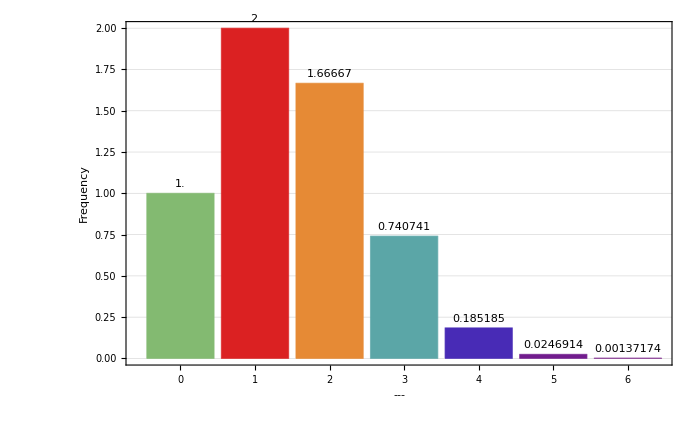

```mathematica
DataAct=Y2
PureData=DataAct[[All,2]]/729.
DataLabels=DataAct[[All,1]]
BarChart[PureData,ChartLabels->Map[Rotate[#,45 Degree]&,DataLabels],GridLines->Automatic,Frame->True,FrameLabel->{"---","Frequency"},ColorFunction->Function[{height},ColorData["Rainbow"][height]],LabelingFunction->(Placed[#,Above]&),PlotRangePadding->Scaled[.05],ImageSize->700]
```

```mathematica
Z1=Table[Select[Map[{Count[#[[1]],a],#[[2]]}&,YYY],#[[1]]===i&],{i,0,6}]
```

{{{0,240},{0,192},{0,160},{0,64},{0,60},{0,12},{0,1}},{{1,480},{1,480},{1,240},{1,192},{1,60},{1,6}},{{2,480},{2,360},{2,240},{2,120},{2,15}},{{3,240},{3,160},{3,120},{3,20}},{{4,60},{4,60},{4,15}},{{5,12},{5,6}},{{6,1}}}

```mathematica
Z2=Map[{#[[1,1]],Total[#[[All,2]]]}&,Z1]
```

{{0,729},{1,1458},{2,1215},{3,540},{4,135},{5,18},{6,1}}

{{0,729},{1,1458},{2,1215},{3,540},{4,135},{5,18},{6,1}}

{729,1458,1215,540,135,18,1}

{0,1,2,3,4,5,6}

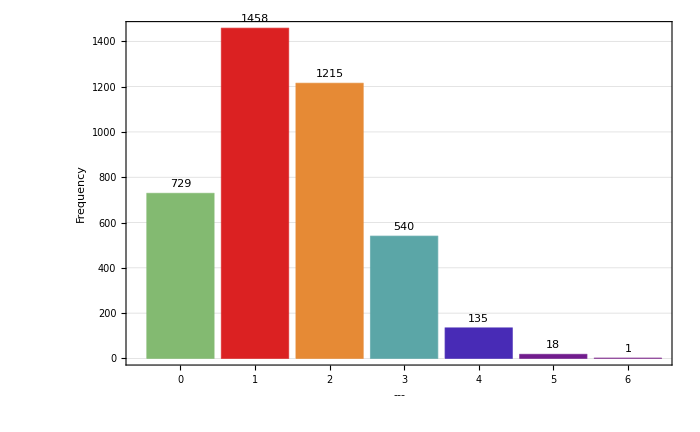

```mathematica
DataAct=Z2
PureData=DataAct[[All,2]]
DataLabels=DataAct[[All,1]]
BarChart[PureData,ChartLabels->Map[Rotate[#,45 Degree]&,DataLabels],GridLines->Automatic,Frame->True,FrameLabel->{"---","Frequency"},ColorFunction->Function[{height},ColorData["Rainbow"][height]],LabelingFunction->(Placed[#,Above]&),PlotRangePadding->Scaled[.05],ImageSize->700]
```

```mathematica
Z2
```

{{0,729},{1,1458},{2,1215},{3,540},{4,135},{5,18},{6,1}}

```mathematica
P[x_,λ_]:=λ^x*ⅇ^-λ/Factorial[x]
```

```mathematica
QF=Total@Map[((P[x,λ]/.x-> #[[1]])-#[[2]])^2&,Z2]
```

(-729+ⅇ^-λ)^2+(-1458+ⅇ^-λ λ)^2+(-1215+1/2 ⅇ^-λ λ^2)^2+(-540+1/6 ⅇ^-λ λ^3)^2+(-135+1/24 ⅇ^-λ λ^4)^2+(-18+1/120 ⅇ^-λ λ^5)^2+(-1+1/720 ⅇ^-λ λ^6)^2

```mathematica
NMinimize[QF,λ]
```

{4.44145×10^6,{λ→1.06471}}

```mathematica
P[x,1.0647062383249333]
```

(0.344829 1.06471^x)/(x!)

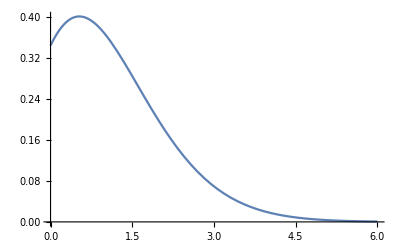

```mathematica
Plot[1*P[x,1.0647062383249333],{x,0,6}]
```

```mathematica
BarChart[PureData,ChartLabels->Map[Rotate[#,45 Degree]&,DataLabels],GridLines->Automatic,Frame->True,FrameLabel->{"---","Frequency"},ColorFunction->Function[{height},ColorData["Rainbow"][height]],LabelingFunction->(Placed[#,Above]&),PlotRangePadding->Scaled[.05],ImageSize->700]
```

-Graphics-

```mathematica
Total[Z2[[All,2]]]
```

4096

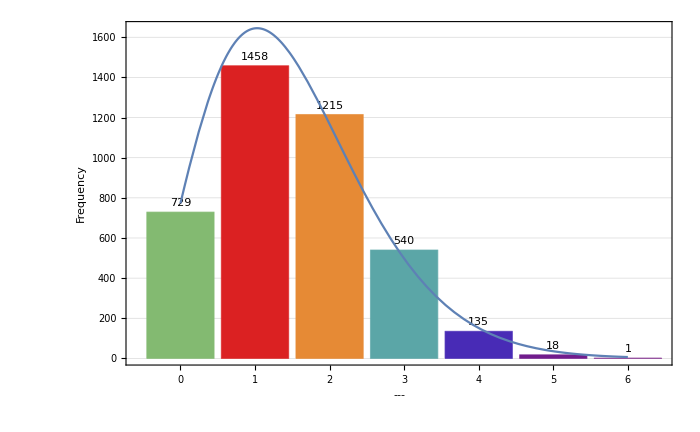

```mathematica
Show[{BarChart[PureData,ChartLabels->Map[Rotate[#,45 Degree]&,DataLabels],GridLines->Automatic,Frame->True,FrameLabel->{"---","Frequency"},ColorFunction->Function[{height},ColorData["Rainbow"][height]],LabelingFunction->(Placed[#,Above]&),PlotRangePadding->Scaled[.05],ImageSize->700],Plot[4096*P[x-1.5,1.0647062383249333],{x,1,7}]}]
```

```mathematica
?*FindDistribution
```

```mathematica
Z2[[All,2]]
```

{729,1458,1215,540,135,18,1}

```mathematica
FindDistribution[Z2[[All,2]],10,{All}]
%//MatrixForm
```

{{DataDistribution[…],{1.,1.,-4.12332,-0.558487,-6.74495,-1.94591,{15,1.94591},-6.95289,-6.95289,15}},{GeometricDistribution[0.00161754],{0.446374,0.63564,-14.7636,-15.1482,-14.9384,-7.37411,{1,7.37411},-15.354,-15.354,1}},{DiscreteUniformDistribution[{1,1458}],{0.446403,0.32717,-14.5851,-14.9696,-14.7599,-7.28482,{1,7.28482},-15.6713,-15.6713,1}},{BenfordDistribution[1459],{0.159916,0.0759007,-14.1203,-14.5049,-14.2951,-7.05245,{1,7.05245},-15.7842,-15.7842,1}},{LogSeriesDistribution[0.999811],{0.451259,0.189273,-14.553,-14.9375,-14.7277,-7.26877,{1,7.26877},-16.2169,-16.2169,1}},{ZipfDistribution[0.190515],{0.015938,0.207467,-15.4725,-15.8571,-15.6473,-7.72854,{1,7.72854},-16.5516,-16.5516,1}},{WaringYuleDistribution[0.19084],{0.0156013,0.186398,-15.6993,-16.0839,-15.8741,-7.84194,{1,7.84194},-16.7855,-16.7855,1}},{DataDistribution[…],{0.683371,0.359134,-15.0892,-25.012,-15.9631,-7.50602,{5,7.50602},-17.3805,-17.3805,5}},{PoissonDistribution[617.222],{0.0608855,0.0208283,-599.642,-600.026,-599.816,-299.813,{1,299.813},-599.925,-599.925,1}},{BinomialDistribution[1469,0.420165],{0.0281953,0.0209267,Indeterminate,Indeterminate,Indeterminate,Indeterminate,{2,Indeterminate},Indeterminate,Indeterminate,2}}}

(DataDistribution[…] | {1.,1.,-4.12332,-0.558487,-6.74495,-1.94591,{15,1.94591},-6.95289,-6.95289,15}
GeometricDistribution[0.00161754] | {0.446374,0.63564,-14.7636,-15.1482,-14.9384,-7.37411,{1,7.37411},-15.354,-15.354,1}
DiscreteUniformDistribution[{1,1458}] | {0.446403,0.32717,-14.5851,-14.9696,-14.7599,-7.28482,{1,7.28482},-15.6713,-15.6713,1}
BenfordDistribution[1459] | {0.159916,0.0759007,-14.1203,-14.5049,-14.2951,-7.05245,{1,7.05245},-15.7842,-15.7842,1}
LogSeriesDistribution[0.999811] | {0.451259,0.189273,-14.553,-14.9375,-14.7277,-7.26877,{1,7.26877},-16.2169,-16.2169,1}
ZipfDistribution[0.190515] | {0.015938,0.207467,-15.4725,-15.8571,-15.6473,-7.72854,{1,7.72854},-16.5516,-16.5516,1}
WaringYuleDistribution[0.19084] | {0.0156013,0.186398,-15.6993,-16.0839,-15.8741,-7.84194,{1,7.84194},-16.7855,-16.7855,1}
DataDistribution[…] | {0.683371,0.359134,-15.0892,-25.012,-15.9631,-7.50602,{5,7.50602},-17.3805,-17.3805,5}
PoissonDistribution[617.222] | {0.0608855,0.0208283,-599.642,-600.026,-599.816,-299.813,{1,299.813},-599.925,-599.925,1}
BinomialDistribution[1469,0.420165] | {0.0281953,0.0209267,Indeterminate,Indeterminate,Indeterminate,Indeterminate,{2,Indeterminate},Indeterminate,Indeterminate,2})